```mathematica
g=9.81;
ρ=1.2;
m=4/7000;
r=38/2000;
τ=0.65;
veq=2.8;
```

```mathematica
A=π r^2
Vb=4/3 π r^3
b=(2 g)/veq((m-ρ Vb)/m)
```

(361 π)/1000000

(6859 π)/750000000

6.58437

```mathematica
ω=1;
ζ=1;
```

```mathematica
θ10=-ω^2/b
θ20=(2 ζ ω-b)/b
```

-0.151875

-0.69625

```mathematica
tf=1000;
```

```mathematica
uc[t_]=If[Sin[2π t/30]≥0,0.1,0.2];
```

```mathematica
solm=First[NDSolve[{yms''[t]==-2 ζ ω yms'[t]-ω^2 yms[t]+ω^2 uc[t],yms'[0]==0,yms[0]==0},yms,{t,0,tf}]]
```

{yms→InterpolatingFunction[…]}

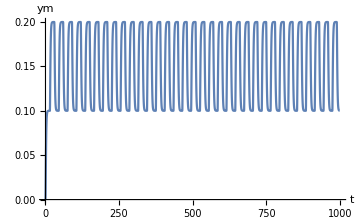

```mathematica
Plot[yms[t]/. solm,{t,0,tf},PlotRange->All,ImageSize->Medium,AxesLabel->{"t","ym"}]
```

```mathematica
γ={100,200,400,1000};
solL=Table[First[NDSolve[{ys''[t]==-b(1+θ2[t]) ys'[t]+b θ1[t] ys[t]-b θ1[t] uc[t],θ1'[t]==-γ⟦i⟧(ys[t]-uc[t]) (ys'[t]-yms'[t]),θ2'[t]==γ⟦i⟧ys'[t] (ys'[t]-yms'[t]),ys[0]==0,ys'[0]==0,θ1[0]==0,θ2[0]==0}/. solm,{ys,θ1,θ2},{t,0,tf}]],{i,Length[γ]}]
```

{{ys→InterpolatingFunction[…],θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…]},{ys→InterpolatingFunction[…],θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…]},{ys→InterpolatingFunction[…],θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…]},{ys→InterpolatingFunction[…],θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…]}}

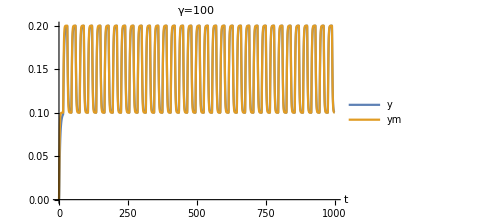
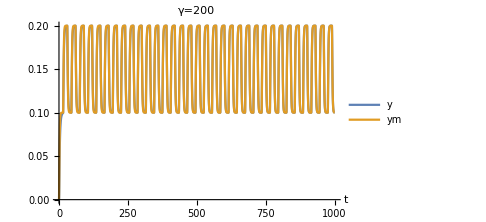
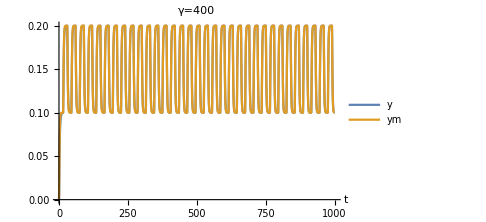
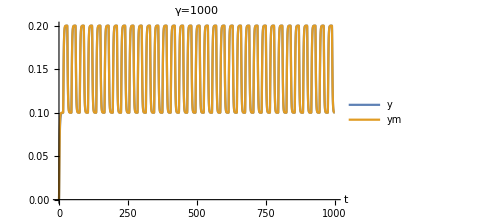

```mathematica
Table[Plot[Evaluate[{ys[t],yms[t]}/. Join[solL⟦i⟧,solm]],{t,0,tf},PlotRange->All,PlotLegends->{"y","ym"},AxesLabel->{"t",""},ImageSize->Medium,PlotLabel->"γ="<>ToString[γ⟦i⟧]],{i,Length[solL]}]
```

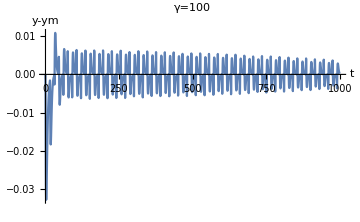
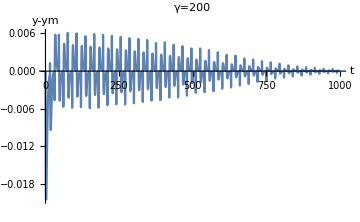
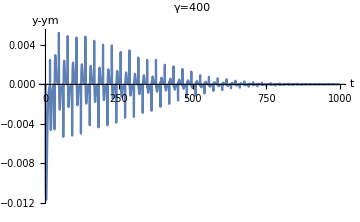
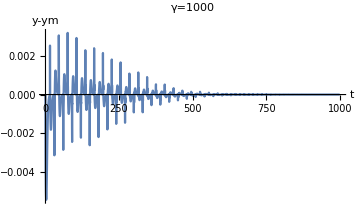

```mathematica
Table[Plot[Evaluate[ys[t]-yms[t]/. Join[solL⟦i⟧,solm]],{t,0,tf},PlotRange->All,AxesLabel->{"t","y-ym"},ImageSize->Medium,PlotLabel->"γ="<>ToString[γ⟦i⟧]],{i,Length[solL]}]
```

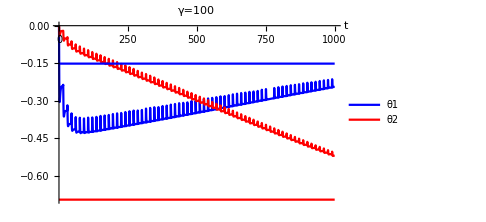
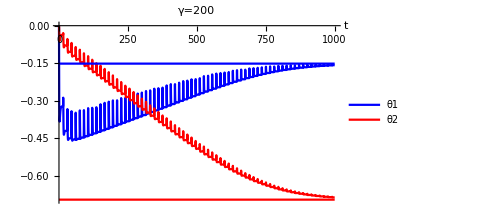
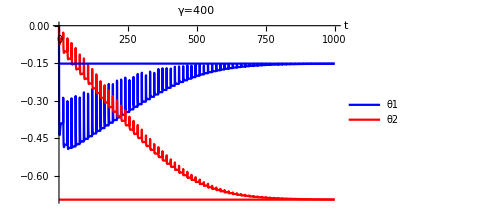
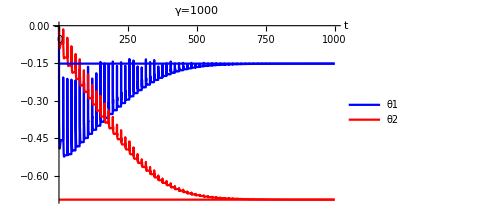

```mathematica
Table[Plot[Evaluate[Join[{θ1[t],θ2[t]}/. solL⟦i⟧,{θ10,θ20}]],{t,0,tf},PlotLegends->{"θ1","θ2"},AxesLabel->{"t",""},ImageSize->Medium,PlotLabel->"γ="<>ToString[γ⟦i⟧],PlotStyle->{Blue,Red},PlotRange->All],{i,Length[solL]}]
```

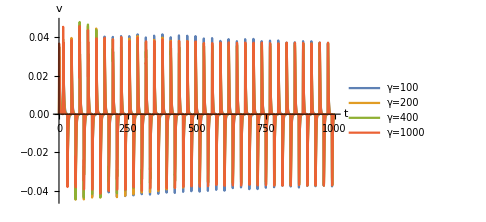

```mathematica
Plot[Evaluate[Table[(θ1[t] (ys[t]-uc[t])-θ2[t] ys'[t])/. solL⟦i⟧,{i,Length[γ]}]],{t,0,tf},AxesLabel->{"t","v"},PlotRange-> All,PlotLegends->Table["γ="<>ToString[γ⟦i⟧],{i,Length[γ]}],ImageSize->Medium]
```

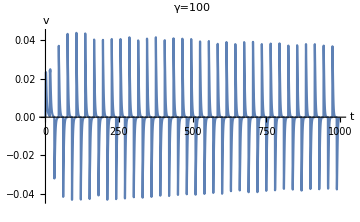
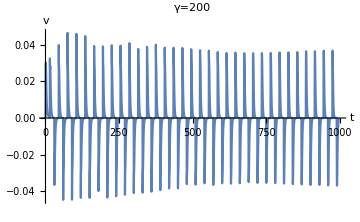
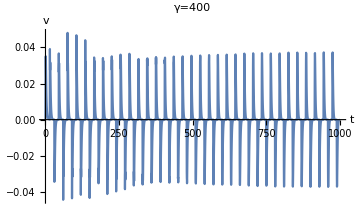
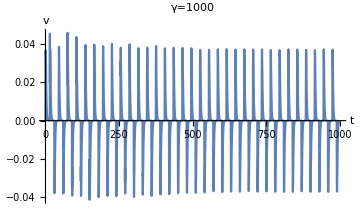

```mathematica
Table[Plot[Evaluate[(θ1[t] (ys[t]-uc[t])-θ2[t] ys'[t])/. Join[solL⟦i⟧,solm]],{t,0,tf},PlotRange->All,AxesLabel->{"t","v"},ImageSize->Medium,PlotLabel->"γ="<>ToString[γ⟦i⟧]],{i,Length[solL]}]
```

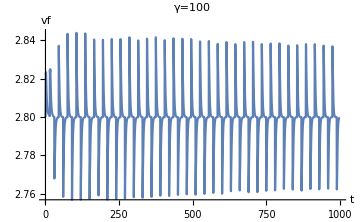
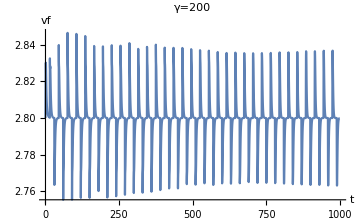
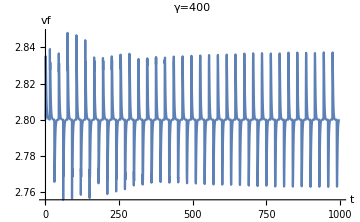
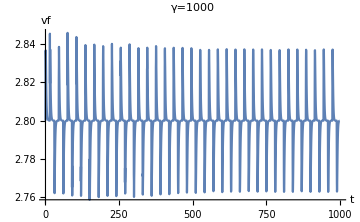

```mathematica
Table[Plot[Evaluate[(θ1[t] (ys[t]-uc[t])-θ2[t] ys'[t])+veq/. Join[solL⟦i⟧,solm]],{t,0,tf},PlotRange->All,AxesLabel->{"t","vf"},ImageSize->Medium,PlotLabel->"γ="<>ToString[γ⟦i⟧]],{i,Length[solL]}]
```

```mathematica
γ[[1]]
```

100